```mathematica
Grid[Table[i*j,{i,12},{j,12}]]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144

```mathematica
Manipulate[Grid[Table[i*j,{i,n},{j,n}]],{n,Range[12]}]
```

```mathematica
RomanNumeral[1]
```

I

```mathematica
Grid[Table[RomanNumeral[i*j],{i,5},{j,5}]]
```

I | II | III | IV | V
II | IV | VI | VIII | X
III | VI | IX | XII | XV
IV | VIII | XII | XVI | XX
V | X | XV | XX | XXV

```mathematica
Manipulate[Grid[Table[RomanNumeral[i*j],{i,n},{j,n}]],{n,1,5}]
```

```mathematica
Manipulate[Row[{Grid[Table[i*j,{i,n},{j,n}]],Grid[Table[RomanNumeral[i*j],{i,n},{j,n}]]},"  |  ",Frame->True,FrameMargins->10,Background->LightBlue],{n,1,10},FrameMargins->10]
```

```mathematica
Grid[Table[RandomColor[],10,10]]
```

RGBColor[0.3078754283070566, 0.31824610469322234, 0.09674749153909756] | RGBColor[0.02934059310164172, 0.8336544752115089, 0.6599953181247367] | RGBColor[0.7469447749634917, 0.4119371428315388, 0.19680461540121796] | RGBColor[0.8455902862440974, 0.2291758406710216, 0.6572947867713521] | RGBColor[0.8216555131996355, 0.20280335361853874, 0.12748470434085069] | RGBColor[0.619987129841681, 0.44436406530361605, 0.5038324391837092] | RGBColor[0.15004141973456764, 0.9722714118141147, 0.08343138931776517] | RGBColor[0.18231905810188476, 0.10264856868257688, 0.92652953181333] | RGBColor[0.9584092986690442, 0.7891457425236423, 0.3334318506243701] | RGBColor[0.9952218413941112, 0.6550327765025961, 0.08906901902072906]
RGBColor[0.5456079340609323, 0.5867144364812416, 0.29303694422829873] | RGBColor[0.13015769098567276, 0.3278749004515755, 0.721362135146701] | RGBColor[0.4641862660854581, 0.05078533113440509, 0.6311148879955781] | RGBColor[0.19771487410598287, 0.009882735429969314, 0.43592274323667857] | RGBColor[0.4656746219145944, 0.02481392028510654, 0.11551629650685746] | RGBColor[0.7544075628373463, 0.4148671204442165, 0.3070098840128441] | RGBColor[0.3868557231234495, 0.8760988323460575, 0.6860690471489999] | RGBColor[0.44271224107482965, 0.7635718014107691, 0.6166134447882354] | RGBColor[0.5269184394397166, 0.41929484141417084, 0.7785499530511142] | RGBColor[0.8223651284138442, 0.9654946464468952, 0.6413565219817157]
RGBColor[0.5204499072732649, 0.5453746996185733, 0.9100638940848667] | RGBColor[0.48568122432267447, 0.1406787849426545, 0.09916453737094733] | RGBColor[0.8595360044831051, 0.4450593492530539, 0.021054438876653814] | RGBColor[0.4628971534298598, 0.519505948658826, 0.257418316564771] | RGBColor[0.1734513996120579, 0.6366949518119847, 0.03388790997110602] | RGBColor[0.038079685416191555, 0.7673557907888584, 0.6970976460898233] | RGBColor[0.5226550501305656, 0.5369684983690748, 0.8976173159170397] | RGBColor[0.4984460474460095, 0.01214322632745568, 0.36436004352401685] | RGBColor[0.9003342016960587, 0.5370132169714745, 0.32404652222136976] | RGBColor[0.19993639331666735, 0.6407579103645997, 0.2214924397556992]
RGBColor[0.7443522246540757, 0.40623270701187075, 0.5862768812066224] | RGBColor[0.260253644393851, 0.6017189647105718, 0.3765278749864287] | RGBColor[0.9209838173244149, 0.4038304257043628, 0.3666492075567096] | RGBColor[0.3391160381942586, 0.046866016182119496, 0.8914289458192115] | RGBColor[0.851761318006407, 0.6260260574903378, 0.11531636647691146] | RGBColor[0.44679224230490244, 0.36343531720577715, 0.8692756834198136] | RGBColor[0.5653318427814333, 0.6051201484847943, 0.5743351656506093] | RGBColor[0.9527095316917116, 0.5636831493363124, 0.229157097168309] | RGBColor[0.8486268027911972, 0.33079375087421936, 0.6616322510563784] | RGBColor[0.7180936237557667, 0.09501667475098285, 0.37786942286885994]
RGBColor[0.4381819784966532, 0.6803072786524134, 0.2598653544167706] | RGBColor[0.58363937026675, 0.0315977597696655, 0.5805547302874392] | RGBColor[0.49961021882598944, 0.168596988323243, 0.13254957604356354] | RGBColor[0.7600965386134533, 0.6812785311140896, 0.3196348208741788] | RGBColor[0.8178719615901044, 0.4981678045409743, 0.5833931993052761] | RGBColor[0.10965290296180186, 0.8607196550475054, 0.3270921338547297] | RGBColor[0.910569334166683, 0.8222847963112709, 0.5730435343954274] | RGBColor[0.3891326482894384, 0.6301974208406438, 0.26001601699314203] | RGBColor[0.3729334828021571, 0.41553918428319614, 0.4459734579543624] | RGBColor[0.5305289519111902, 0.5336437165544281, 0.62193489515234]
RGBColor[0.0822704553114122, 0.6152402372932402, 0.3593284986766696] | RGBColor[0.733092807501794, 0.03554473379932577, 0.9081285224084312] | RGBColor[0.6912544545372901, 0.465419509762903, 0.37200464727747007] | RGBColor[0.06675606124581179, 0.30557195925437597, 0.8010837057405005] | RGBColor[0.6828206679804507, 0.9845218181542643, 0.03780030348895713] | RGBColor[0.9085901565206089, 0.553571494303009, 0.194918170330159] | RGBColor[0.8996629447525171, 0.7620871582763304, 0.18746849777452934] | RGBColor[0.5428355769063902, 0.15830479873471948, 0.712553343527299] | RGBColor[0.04870491775323238, 0.14618898139863834, 0.6387002592037445] | RGBColor[0.14873465864553137, 0.6774205206518855, 0.926715888630012]
RGBColor[0.012249330033253125, 0.2017071474514498, 0.45311512063357684] | RGBColor[0.33505085500263987, 0.2563958661861434, 0.642778176887699] | RGBColor[0.7669696867839728, 0.32147839025914626, 0.4013525784881635] | RGBColor[0.8129420194670727, 0.630307682301328, 0.5391573660631614] | RGBColor[0.1520428252125643, 0.30586998071822924, 0.7462510663507562] | RGBColor[0.5646915832002146, 0.32908229981056425, 0.2771065973300957] | RGBColor[0.1491072439691814, 0.31307782272133067, 0.11851976836921407] | RGBColor[0.2380646715501462, 0.7487566658918985, 0.8542519668007083] | RGBColor[0.6163016625281159, 0.16806269532491735, 0.9892251902327576] | RGBColor[0.2355242407242717, 0.785930990060612, 0.40377341666411715]
RGBColor[0.4570788358945004, 0.6309182810827929, 0.06614522902176212] | RGBColor[0.044851817585092935, 0.6512946319556527, 0.08711412347976699] | RGBColor[0.6961289066769711, 0.09101677341131098, 0.8648693088905552] | RGBColor[0.72845718902169, 0.41221149338932617, 0.4986198740217256] | RGBColor[0.21264051736376155, 0.5570226724503127, 0.7003695601157025] | RGBColor[0.3989205828349278, 0.10710407641410558, 0.2426710566165795] | RGBColor[0.564173377508844, 0.5141603644811397, 0.15335204879661402] | RGBColor[0.2783298342208924, 0.7115736011681928, 0.807473330538039] | RGBColor[0.07742496101018981, 0.37535147610949027, 0.6252909351330149] | RGBColor[0.6171656919349391, 0.970219919555624, 0.14205748707155652]
RGBColor[0.8942535539364742, 0.9493222201999247, 0.33461829595643233] | RGBColor[0.3527798920701457, 0.415451350784354, 0.9661035021635529] | RGBColor[0.25216700570736017, 0.6945807139039222, 0.3358477201358152] | RGBColor[0.7391673192434183, 0.9788487708543372, 0.3664522132134589] | RGBColor[0.2754376802895053, 0.46461068618392787, 0.45845908364719845] | RGBColor[0.1991039283679239, 0.9196700275757688, 0.548208024994739] | RGBColor[0.730504377538687, 0.12080858747800183, 0.9757779692647268] | RGBColor[0.18942555205906353, 0.08624447505118926, 0.3487608833914866] | RGBColor[0.3145743709507729, 0.26396966916115994, 0.8487085393168603] | RGBColor[0.9133534899983267, 0.8872253005796304, 0.1412020744787521]
RGBColor[0.8221817625138117, 0.3202713218222928, 0.5027911213468095] | RGBColor[0.07382166408700197, 0.1544170880656084, 0.980295547562793] | RGBColor[0.812105929935089, 0.7286081070175883, 0.062341707352665754] | RGBColor[0.04168245987633501, 0.16660640497356494, 0.041986505554851394] | RGBColor[0.3354219933953895, 0.16647111050494567, 0.28019168008116235] | RGBColor[0.49976025530830115, 0.6906719770341252, 0.7642271599163251] | RGBColor[0.11289611470442718, 0.9947018600704891, 0.959856185924677] | RGBColor[0.9406111982923502, 0.6825187346373844, 0.7068296724904284] | RGBColor[0.9069686685974823, 0.8959401961998141, 0.8618170030605725] | RGBColor[0.6620836305371611, 0.7315761940925936, 0.3614470335223985]

```mathematica
Grid[Table[Style[RandomInteger[10],RandomColor[]],10,10]]
```

1 | 9 | 6 | 10 | 7 | 1 | 8 | 5 | 9 | 6
3 | 3 | 4 | 1 | 8 | 4 | 4 | 9 | 7 | 10
3 | 8 | 0 | 0 | 7 | 8 | 6 | 1 | 0 | 2
5 | 5 | 10 | 2 | 4 | 4 | 9 | 7 | 8 | 0
10 | 3 | 4 | 10 | 10 | 9 | 2 | 2 | 5 | 10
10 | 1 | 10 | 1 | 6 | 3 | 4 | 0 | 6 | 10
8 | 2 | 6 | 9 | 4 | 8 | 1 | 9 | 10 | 6
3 | 4 | 0 | 10 | 8 | 10 | 2 | 3 | 9 | 3
6 | 8 | 1 | 8 | 10 | 5 | 1 | 10 | 3 | 2
1 | 6 | 1 | 1 | 10 | 2 | 5 | 7 | 8 | 0

```mathematica
data = {1,4,3,5,2}
```

{1,4,3,5,2}

```mathematica
Grid[Table[func[data],1,{func,{PieChart,NumberLinePlot,ListLinePlot,BarChart}}]]
```

-Graphics-

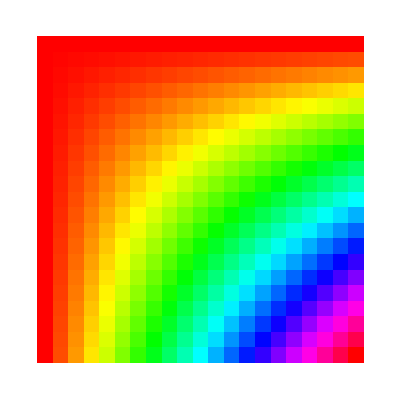

```mathematica
ArrayPlot[Table[Hue[x*y],{x,0,1,.05},{y,0,1,.05}]]
```

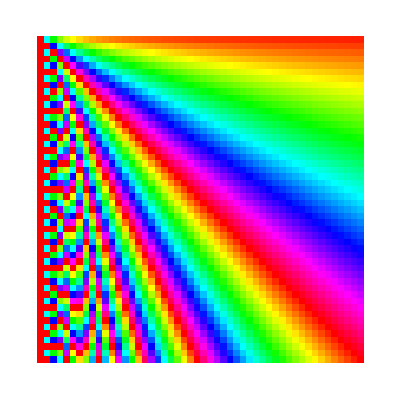

```mathematica
ArrayPlot[Table[Hue[x/y],{x,1,50},{y,1,50}]]
```

```mathematica
ArrayPlot[Table[StringLength[RomanNumeral[i*j]],{i,100},{j,100}]]
```

-Graphics-

```mathematica
Grid[Table[Style[RandomInteger[10],RandomColor[],RandomInteger[32]],10,10]]
```

8 | 9 | 1 | 9 | 0 | 3 | 5 | 9 | 5 | 6
1 | 6 | 3 | 4 | 1 | 4 | 0 | 0 | 2 | 0
2 | 5 | 3 | 9 | 10 | 5 | 6 | 0 | 10 | 7
6 | 3 | 4 | 9 | 0 | 10 | 10 | 5 | 3 | 8
0 | 6 | 8 | 1 | 2 | 9 | 2 | 3 | 6 | 5
10 | 4 | 6 | 7 | 5 | 9 | 7 | 0 | 1 | 7
4 | 9 | 5 | 6 | 6 | 1 | 0 | 6 | 3 | 9
9 | 8 | 8 | 9 | 2 | 2 | 7 | 5 | 1 | 8
8 | 0 | 2 | 2 | 5 | 1 | 4 | 1 | 8 | 8
10 | 5 | 8 | 8 | 4 | 7 | 1 | 5 | 1 | 6

```mathematica
Manipulate[Grid[Table[Style[RandomInteger[20],RandomColor[],RandomInteger[size]],number,number]],{number,1,5,1},{size,12,48,4}]
```

```mathematica
Manipulate[Row[{Grid[Table[i*j,{i,n},{j,n}]],Grid[Table[RomanNumeral[i*j],{i,n},{j,n}]]},"  |  ",Frame->True,FrameMargins->10,Background->LightBlue],{n,1,10},FrameMargins->10]
```

```mathematica
Manipulate[ArrayPlot[Table[Hue[x/y],{x,1,n},{y,1,n}]],{n,2,100,1}]
```

```mathematica
Manipulate[ArrayPlot[Table[Hue[x*y],{x,0,1,n},{y,0,1,n}]],{n,.09,.01}]
```